```mathematica
SetDirectory[NotebookDirectory[]];
(*IMPORTAR ARCHIVOS Y EXTRAER T Y SUS*)
DataL10=Import["Promedios-N-10_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL20=Import["Promedios-N-20_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL30=Import["Promedios-N-30_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL40=Import["Promedios-N-40_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL50=Import["Promedios-N-50_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
T10=DataL10[[All,1]];
Sus10 = DataL10[[All,3]];
T20=DataL20[[All,1]];
Sus20 = DataL20[[All,3]];
T30=DataL30[[All,1]];
Sus30 = DataL30[[All,3]];
T40=DataL40[[All,1]];
Sus40 = DataL40[[All,3]];
T50=DataL50[[All,1]];
Sus50 = DataL50[[All,3]];
(*FUNCIONES DE ESCALADO*)
EscT[TC_,ν_,γ_,T_,L_]:=L^(1/ν) (T-TC)/TC;
EscSus[ν_,γ_,Sus_,L_]:=L^(-γ/ν) Sus;
(*FUNCIÓN QUE CREA UN VECTOR DE N VECTORES DE 2 COMPONENTES (T ESCALADA y SUS ESCALDA) PARA REPRESENTARLOS*)
Graphic[TC_,ν_,γ_,T_,Sus_,L_]:=Transpose[{EscT[TC,ν,γ,T,L],EscSus[ν,γ,Sus,L]}];
(*CREACIÓN DE LA GRÁFICA*)
Manipulate[ListPlot[{
Graphic[TC,ν,γ,T10,Sus10,10],
Graphic[TC,ν,γ,T20,Sus20,20],
Graphic[TC,ν,γ,T30,Sus30,30],
Graphic[TC,ν,γ,T40,Sus40,40],
Graphic[TC,ν,γ,T50,Sus50,50]
},PlotRange->{{-5,7},All},PlotStyle->Thick, PlotTheme->"Scientific", FrameLabel->{"Temperatura", "Magnetización en valor absoluta"}, Axes->True]
,"T_c"->{TC,2,3},"ν"->{ν,0.7,1.2},"γ"->{γ,-2,0}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*IMPORTAR ARCHIVOS Y EXTRAER T Y SUS*)
DataL10=Import["Promedios-N-10_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
(*DataL20=Import["Promedios-N-20_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];*)
DataL30=Import["Promedios-N-30_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL40=Import["Promedios-N-40_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL50=Import["Promedios-N-50_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
T10=DataL10[[All,1]];
Sus10 = DataL10[[All,2]];
T20=DataL20[[All,1]];
Sus20 = DataL20[[All,2]];
T30=DataL30[[All,1]];
Sus30 = DataL30[[All,2]];
T40=DataL40[[All,1]];
Sus40 = DataL40[[All,2]];
T50=DataL50[[All,1]];
Sus50 = DataL50[[All,2]];
(*FUNCIONES DE ESCALADO*)
EscT[TC_,ν_,γ_,T_,L_]:=L^(1/ν) (T-TC)/TC;
EscSus[ν_,γ_,Sus_,L_]:=L^(-γ/ν) Sus;
(*FUNCIÓN QUE CREA UN VECTOR DE N VECTORES DE 2 COMPONENTES (T ESCALADA y SUS ESCALDA) PARA REPRESENTARLOS*)
Graphic[TC_,ν_,γ_,T_,Sus_,L_]:=Transpose[{EscT[TC,ν,γ,T,L],EscSus[ν,γ,Sus,L]}];
(*CREACIÓN DE LA GRÁFICA*)
Manipulate[ListPlot[{
Graphic[TC,ν,γ,T10,Sus10,10]

},PlotRange->{{-5,7},All},PlotStyle->Thick, Joined->True]
,"T_c"->{TC,2,3},"ν"->{ν,0.7,1.2},"γ"->{γ,1.1,1.8}]
```

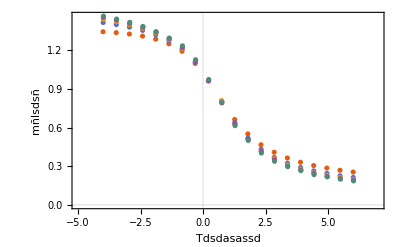

```mathematica
ListPlot[{
Graphic[2.26912,1, -0.132,T10,Sus10,10],
Graphic[2.26912,1, -0.132,T20,Sus20,20],
Graphic[2.26912,1, -0.132,T30,Sus30,30],
Graphic[2.26912,1, -0.132,T40,Sus40,40],
Graphic[2.26912,1, -0.132,T50,Sus50,50]
},PlotRange->{{-5,7},All},PlotStyle->Thick, PlotTheme->"Scientific", AxesLabel->{"Tdsdasassd", "mñlsdsñ"}, Axes->True]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*IMPORTAR ARCHIVOS Y EXTRAER T Y SUS*)
DataL10=Import["Promedios-N-10_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL20=Import["Promedios-N-20_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL30=Import["Promedios-N-30_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL40=Import["Promedios-N-40_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL50=Import["Promedios-N-50_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
T10=DataL10[[All,1]];
Sus10 = DataL10[[All,5]];
T20=DataL20[[All,1]];
Sus20 = DataL20[[All,5]];
T30=DataL30[[All,1]];
Sus30 = DataL30[[All,5]];
T40=DataL40[[All,1]];
Sus40 = DataL40[[All,5]];
T50=DataL50[[All,1]];
Sus50 = DataL50[[All,5]];
(*FUNCIONES DE ESCALADO*)
EscT[TC_,ν_,γ_,T_,L_]:=L^(1/ν) (T-TC)/TC;
EscSus[ν_,γ_,Sus_,L_]:=L^(-γ/ν) Sus;
(*FUNCIÓN QUE CREA UN VECTOR DE N VECTORES DE 2 COMPONENTES (T ESCALADA y SUS ESCALDA) PARA REPRESENTARLOS*)
Graphic[TC_,ν_,γ_,T_,Sus_,L_]:=Transpose[{EscT[TC,ν,γ,T,L],EscSus[ν,γ,Sus,L]}];
(*CREACIÓN DE LA GRÁFICA*)
Manipulate[ListPlot[{
Graphic[TC,ν,γ,T10,Sus10,10],
Graphic[TC,ν,γ,T20,Sus20,20],
Graphic[TC,ν,γ,T30,Sus30,30],
Graphic[TC,ν,γ,T40,Sus40,40],
Graphic[TC,ν,γ,T50,Sus50,50]
},PlotRange->{{-5,7},All},PlotStyle->Thick, PlotTheme->"Scientific", FrameLabel->{"Temperatura", "Susceptibilidad"}, Axes->True]
,"T_c"->{TC,2,3},"ν"->{ν,0.7,1.2},"γ"->{γ,1.5,2}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*IMPORTAR ARCHIVOS Y EXTRAER T Y SUS*)
DataL10=Import["Promedios-N-10_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL20=Import["Promedios-N-20_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL30=Import["Promedios-N-30_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL40=Import["Promedios-N-40_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL50=Import["Promedios-N-50_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
T10=DataL10[[All,1]];
Sus10 = DataL10[[All,6]];
T20=DataL20[[All,1]];
Sus20 = DataL20[[All,6]];
T30=DataL30[[All,1]];
Sus30 = DataL30[[All,6]];
T40=DataL40[[All,1]];
Sus40 = DataL40[[All,6]];
T50=DataL50[[All,1]];
Sus50 = DataL50[[All,6]];
(*FUNCIONES DE ESCALADO*)
EscT[TC_,ν_,γ_,T_,L_]:=L^(1/ν) (T-TC)/TC;
EscSus[ν_,γ_,Sus_,L_]:=L^(-γ/ν) Sus;
(*FUNCIÓN QUE CREA UN VECTOR DE N VECTORES DE 2 COMPONENTES (T ESCALADA y SUS ESCALDA) PARA REPRESENTARLOS*)
Graphic[TC_,ν_,γ_,T_,Sus_,L_]:=Transpose[{EscT[TC,ν,γ,T,L],EscSus[ν,γ,Sus,L]}];
(*CREACIÓN DE LA GRÁFICA*)
Manipulate[ListPlot[{
Graphic[TC,ν,γ,T10,Sus10,10],
Graphic[TC,ν,γ,T20,Sus20,20],
Graphic[TC,ν,γ,T30,Sus30,30],
Graphic[TC,ν,γ,T40,Sus40,40],
Graphic[TC,ν,γ,T50,Sus50,50]
},PlotRange->{{-5,7},All},PlotStyle->Thick, PlotTheme->"Scientific", FrameLabel->{"Temperatura", "Energía"}, Axes->True]
,"T_c"->{TC,2,3},"ν"->{ν,0.7,1.2},"γ"->{γ,1.5,2.5}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*IMPORTAR ARCHIVOS Y EXTRAER T Y SUS*)
DataL10=Import["Promedios-N-10_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL20=Import["Promedios-N-20_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL30=Import["Promedios-N-30_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL40=Import["Promedios-N-40_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
DataL50=Import["Promedios-N-50_Nmed-500000.csv","CSV","HeaderLines"->1,Delimiter->","];
T10=DataL10[[All,1]];
Sus10 = DataL10[[All,8]];
T20=DataL20[[All,1]];
Sus20 = DataL20[[All,8]];
T30=DataL30[[All,1]];
Sus30 = DataL30[[All,8]];
T40=DataL40[[All,1]];
Sus40 = DataL40[[All,8]];
T50=DataL50[[All,1]];
Sus50 = DataL50[[All,8]];
(*FUNCIONES DE ESCALADO*)
EscT[TC_,ν_,γ_,T_,L_]:=L^(1/ν) (T-TC)/TC;
EscSus[ν_,γ_,Sus_,L_]:=L^(-γ/ν) Sus;
(*FUNCIÓN QUE CREA UN VECTOR DE N VECTORES DE 2 COMPONENTES (T ESCALADA y SUS ESCALDA) PARA REPRESENTARLOS*)
Graphic[TC_,ν_,γ_,T_,Sus_,L_]:=Transpose[{EscT[TC,ν,γ,T,L],EscSus[ν,γ,Sus,L]}];
(*CREACIÓN DE LA GRÁFICA*)
Manipulate[ListPlot[{
Graphic[TC,ν,γ,T10,Sus10,10],
Graphic[TC,ν,γ,T20,Sus20,20],
Graphic[TC,ν,γ,T30,Sus30,30],
Graphic[TC,ν,γ,T40,Sus40,40],
Graphic[TC,ν,γ,T50,Sus50,50]
},PlotRange->{{-5,7},All},PlotStyle->Thick, PlotTheme->"Scientific", FrameLabel->{"Temperatura", "Capacidad calorífica"}, Axes->True]
,"T_c"->{TC,2,3},"ν"->{ν,0.7,1.2},"γ"->{γ,0,0.5}]
```